```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
(* trigger autoload Failure formatting *)
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

## update

```mathematica
PacletUninstall["CodeInspector"]
```

```mathematica
PacletInstall["/Users/brenton/development/stash/COD/codeinspector/build/paclet/CodeInspector-999.paclet"]
```

PacletObject[CodeInspector,999,<>]

```mathematica
PacletDirectoryAdd["/Users/brenton/development/stash/COD/codeinspector/CodeInspector"];
```

```mathematica
FindFile["CodeInspector`"]
```

/Users/brenton/development/stash/COD/lint/Lint/Kernel/Lint.wl

```mathematica
PacletUpdate["CodeInspector","UpdateSites"->True]
```

PacletObject[Lint,0.15,<>]

## Pre Init: Setup System` symbols

```mathematica
Needs["Lint`"]
```

```mathematica
Lint`AbstractRules`setupSystemSymbols[]//AbsoluteTiming
```

{35.7659,Null}

## Init

```mathematica
$MessagePrePrint=.
```

```mathematica
Off[General::stop]
```

The AST package must be built first. Change these paths to point to your location of ASTTools.

```mathematica
Needs["CodeInspector`"]
Needs["CodeInspector`ImplicitTimes`"]
```

```mathematica
installation=$InstallationDirectory<>"/";
```

```mathematica
protos="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/";
```

```mathematica
stash="/Users/brenton/development/stash/";
```

```mathematica
cvs="/Users/brenton/development/cvs-development/";
```

```mathematica
github="/Users/brenton/development/github-development/";
```

```mathematica
other="/Users/brenton/development/other-development/";
```

```mathematica
examples="/Users/brenton/Downloads/WLCodeExamples/";
```

```mathematica
(*lineHashExclusions=<|
(*kernelMain / protos*)
"Kernel/StartUp/Algebra/NumberField.m"->{"03d1240b54171896"},
"Kernel/StartUp/Control/CodeGeneration.m"->{"19412d627d6b7e46","694323f420e68a25"},
"Kernel/StartUp/Convert/NBMLConvert.m"->{"31f2e8ea294f80bd"},
"Kernel/StartUp/DataPaclets/PsychrometricPropertyData.m"->{"6999fce83dac548b","62238af94392477c","5f23d2758de3a21f",
"40f8d6c9b6d4b08a"},
"Kernel/StartUp/DateTime/CalendarAstronomy.m"->{"31a45a1c1b35fda4","173ed72efc7557a7"},
"Kernel/StartUp/DSolve/DSolveIntegroDifferentialEquation.m"->{"70806c5ac6cccbc6"},
"Kernel/StartUp/Explore/Explore.m"->{"204f684487679053"},
"Kernel/StartUp/Explore/PlotExplorer.m"->{"04983530c6c11391"},
"Kernel/StartUp/FunctionInterpolation.m"->{"4599dd69670d0292"},
"Kernel/StartUp/GIS/GeoModel.m"->{"1c27000519cde9ed","10c8a44b236ba029","62d9fd8900ee8261"},
"Kernel/StartUp/GIS/GeoProjections.m"->{"7a14bc508f22709f","16911bb751b91ee7","4ab33b1dd799a83b","0637c66fd64e707e","4ab33b1dd799a83b",
"7b1ba946278cbf17","069bf6e928e916b2","3ad653f01f4d5f33","27b3a9c0108ed1d9","466dc1ee9093b6db","6635fbe2602a13ba"},
"Kernel/StartUp/Graphics/GraphicsFormat.m"->{"3f105940ae99f908","5024bd6c9eeaa56a","073b391afdc9e837","6440cadea419ea41","2c1db2175672be73"},
"Kernel/StartUp/ImageProcessing/CompositionOps/Compose.m"->{"3fb6e2e0b3ea6a14"},
"Kernel/StartUp/ImageProcessing/Matrices/Common.m"->{"76146a30598981ea","7b13c36587c903e0","6efd63b1fabadf50","78abe098d3fa2871"},
"Kernel/StartUp/Integrate/trig.m"->{"312f6a2a05f7a632"},
"Kernel/StartUp/LinearAlgebra/TransformConstructors.m"->{"014b2c47dae470d2","014b2c47dae470d2","72725bb3496e1116"},
"Kernel/StartUp/Manipulate.m"->{"63c6508d29a231dc","63c6508d29a231dc","21ebb11eb5eb8ff3","3b6779e059e8cafc",
"0c7d9bf871d837b7","50f1486f6187d938","2e8fd78da03300b3","3f745ba41220d3a6","7f9855eae09a71b5","7bd2fd3eff54b2d4","7ffa231626579ddd"},
"Kernel/StartUp/NDSolve/EquationProcessing/DiscontinuityValues.m"->{"5fb198b362503f4b","26468f9b95a56282"},
"Kernel/StartUp/NDSolve/FEM/FEMBoundaryConditions.m"->{"6708e1f79d36c5d2"},
"Kernel/StartUp/NDSolve/FEM/FEMDiscretization.m"->{"63df233ff906cdba","2de223d7462bc969","5377d7bb94813731","31d1946443afe858","39bbde8a59d1cfa1"},
"Kernel/StartUp/NDSolve/FEM/FEMMesh.m"->{"77b81b15ce83c44f","0f0a5515359f1ba1","01d8b85bc47897c6","4ae6660d412a6cf4","7ca7dbcc62b27784"},
"Kernel/StartUp/NDSolve/FEM/PDEParser.m"->{"61d265e8b87ca6f4","6928ae8049c0eb94"},
"Kernel/StartUp/Network/GraphBoxes.m"->{"44471c9adf36998f","41d6756484bc28c1","41d6756484bc28c1"},
"Kernel/StartUp/Network/GraphChart.m"->{"52ad6f2cf8fc9508"},
"Kernel/StartUp/NIntegrate/SimplexQuadrature.m"->{"2a1e92e5bdb9b59f"},
"Kernel/StartUp/Optimization/NMinimize.m"->{"31f2e8ea294f80bd","33c0e18754f1ca87","05fbc58560d62489"},
"Kernel/StartUp/Reduce/Optimization.m"->{"7354fe94335abd0e"},
"Kernel/StartUp/Reduce/Thue.m"->{"273f4daef0b9ac4e"},
"Kernel/StartUp/Reduce/TRoots.m"->{"6bf17ab528ab3634","0ae2ab78930a6b4b"},
"Kernel/StartUp/Regions/Meshes/MeshGraphicsBox.m"->{"15012f9b6e615e3a","4b582a793c7c4e50"},
"Kernel/StartUp/Regions/Meshes/MeshUtilities.m"->{"7f306bf072dd37b5"},
"Kernel/StartUp/Regions/RegionFunctions/RandomPoint.m"->{"4616b599f2fa37d6"},
"Kernel/StartUp/Regions/RegionGraphics/RegionGraphicsBox.m"->{"338667ce2d251209"},
"Kernel/StartUp/Regions/RegionOperations/SRRelations.m"->{"1c8c83222f5d0c82"},
"Kernel/StartUp/Regions/RegionTransforms/AffineTransforms.m"->{"2fc60f01bef7a902","4222fdf69a8baeb0","6d2e16e85a7da416",
"2ea17edaba8aba31"},
"Kernel/StartUp/Regions/RegionUtilities/SpecialRegions.m"->{"33c67ab17bccac81","6f7b9138db2656ae"},
"Kernel/StartUp/RSolve/RecurrenceTable.m"->{"014747e395d6518b"},
"Kernel/StartUp/Sound/AudioCapture.m"->{"70b00628974564e6"},
"Kernel/StartUp/Sound/AudioUtilities.m"->{"0c6bdb7c4ab10f36"},
"Kernel/StartUp/SpatialAnalysis/PointProcesses/PointProcesses.m"->{"40c32a0afe9384af","550af0dedee0afb9","22e6927b43e01027",
"284d0d33f595fcdb","6bd16240c77f9482","03c86d49bde23991","7ca7fd92e93d67f5"},
"Kernel/StartUp/SpecialFunctions/Spheroidal.m"->{"6e16f82800922386","7906253e39b74fd7","08b3b641ba36d555","03167346aea55881",
"76bc31f32ce72935","185c0324aee7fad0","2985a2a42076c0d3","17f8da2ff386525e","7a2d0f7e605f7eef","7497735755f9e9cf","2e3ff306dc7be3cd",
"0bad421509a91f64","2e3ff306dc7be3cd","0bad421509a91f64","78a49a1be39f66ac","2b53ad8ed694d4af","78a49a1be39f66ac","02fde28cdc8f8515",
"02fde28cdc8f8515"},
"Kernel/StartUp/Statistics/ContinuousDistributions/MultinormalDistributions.m"->{"18b70af3b9aa0f27","1023469f6ea06c4a"},
"Kernel/StartUp/Statistics/NonparametricDistributions/HistogramDistribution.m"->{"0fe8fdcd7760d2cb"},
"Kernel/StartUp/Statistics/Solvers/RandomVariate.m"->{"49ab5df2e8ce36ff"},
"Kernel/StartUp/Sum/SumFiniteSpecialRules.m"->{"08dc11ca3cd2fc44","4109b1ef6072f1b5","16132a05552dd3b0","0e1b0aefcfe083c9",
"4d1cc96fc29f93ef","120217d1ac98d252","51c61a396b951c18","050c056a38b6efa2","77da786bdf4b07e7","2388c63276ff1ed8","480b9699e7ec777d",
"0c74efa034f34341","469e6b373339a737","3c9814cf6756ca4a","30db291a9cf2752e"},
"Kernel/StartUp/Sum/SumInfiniteSpecialRules.m"->{"009b8100f4b38d4e","33eec2bfb4fb29be","1c66ca31096b4421","340a70642d837be3",
"1cd1f097208aa8be","1d30b8df4ebb5fc5","3261b5e0bf425424","1668474f3ea06acf","18c21cb746c4956d","01672fe76d75bb57","55e55046d08fb2d9",
"463ff09673a32ef5","5384051f170c90d3","65927912de0c6a4b","1ebf64bb9169f0bf","5b475f05ba1dceb3","3f5cfe0face42598","0dc05741a3d477b5",
"720a18b2fcabb4d3","1e79bc820b2afb07","64bd987050fc090d","5f9b01f249e3fec3","01e966b9ca6dbeca","5bbd805809ab8919","55fa242385113005",
"112c28588b8ebbd5","14b570c669f658c2","7720cbbc036ce346","35e674e891a87962","7e4130936ee98e84","37b3067ce5d305f6","5e74cc8f396822d0",
"309087f00a929548","0f5235e753aa120f","379f64387817033d","36f8a1a0bad13b2f","18884cbd72648cbb","6518ec105bcd8293","73b8a2d10a0b779a",
"393c0afbfddd8109","5bec2a3708ed6cf8","544eca99045d98c0","35d50fa3cc60d710","0af15edc3a2ea149","2a2c4348641806bc","6d1f39199d250a45",
"29c090d03c69b7d8","0430419de17637a3","1f78eca9ca7a4729","2e552ed214f34275","5d882a9a6b0ac211","3419bf4dc8f7dfec","6b0844d984ad016a",
"0921cd365e323fde"},
"Kernel/StartUp/SymbolicTensors/SymbolicTensors.m"->{"05fec030e95e6476","3eb8e9739ab3e438"},
"Kernel/StartUp/Typeset/Dynamic.m"->{"57f673e76ea2cc7c","72b37c39f1696743","289982d63417f317"},
"Kernel/StartUp/Typeset/TypesetInit.m"->{"11e7d903a5843287","7373773d50cfdf2a"},
"Kernel/StartUp/Typeset/SpokenString.m"->{"33a602646fbb3c07"},
"Kernel/StartUp/Visualization/BarChart3D.m"->{"3203e7bd35a5e4f0","3203e7bd35a5e4f0","7dcd17b4dc392932"},
"Kernel/StartUp/Visualization/Gauges.m"->{"39f354a522826d6a","30fbab6141beb9a6","4482be4096d686e0","72fcd59133313277",
"59ac5f4b7d8f64c8","324903fb58803084","500eed1e82e8688b","02031082ce4514d7"},
"Kernel/StartUp/Wavelets/BattleLemarieWavelet.m"->{"49037cf904a93e45","3b8fe5be4be833ef"},
"Kernel/StartUp/Wavelets/LiftingFilter.m"->{"38731099c22fe90d"},
"Messages/errmsg.m"->{"70e96836925e4183","68022076f22e34f1","0ca5c2437e5f1330","1ed9c6e1816179a3","414b1647a49bb7fd","026120075106fd13",
"0b886d39b01873a7"},

(* installation *)
"AddOns/Applications/CompiledFunctionTools/CompiledFunctionTools.m"->{"0da7a7d28cfca989"},
"AddOns/Applications/CompiledFunctionTools/PrintCode.m"->{"2ee70999758761e4"},
"AddOns/ExtraPackages/DifferentialEquations/NDSolveProblems.m"->{},
"AddOns/Packages/Combinatorica/Combinatorica.m"->{"4c77ed39f6de1bbf"},
"AddOns/Packages/FiniteFields/FiniteFields.m"->{"2b861e17c93dc12a","017a494002e954e2"},
"AddOns/Packages/FourierSeries/FourierSeries.m"->{},
"AddOns/Packages/LinearRegression/LinearRegression.m"->{"2a72cde271a6182f"},
"AddOns/Packages/MultivariateStatistics/MultiDescriptiveStatistics.m"->{"18fdc749f03c0145"},
"AddOns/Packages/NonlinearRegression/NonlinearRegression.m"->{"781b523611463a94"},
"AddOns/Packages/Splines/Splines.m"->{"3bbaf0e5bd799e3c"},
"AddOns/Packages/VariationalMethods/VariationalMethods.m"->{"639685c94ca4306e"},
"SystemFiles/Components/CCodeGenerator/CCodeGenerator.m"->{"78497442d3f98d1b"},
"SystemFiles/Components/Compile/AST/Macro/Builtin/Conditional.m"->{"1d73c3819ade1768","1e0ad42179349164","0db845947764e204",
"0bf9ba4da619f4a3"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Break.m"->{"64499f2d5c2d329e"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Continue.m"->{"335607c5839b8cbf"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Return.m"->{"3b9c3fb7da3d5426"},
"SystemFiles/Components/Compile/Utilities/Language/SymbolAreasTable.m"->{"55eac21c2ba1bb7f","2d3d344d0445c106",
"42f97ad40a0821d4"},
"SystemFiles/Components/CompileUtilities/RuntimeChecks/RuntimeChecks.m"->{"0f40561fc4b61bbe","2dfea9ca8b7e9ec2",
"54d7b7b60d50741a","10c16e404e4c7412","165bc22739e6fa11","0f831b782569644e"},
"SystemFiles/Components/FunctionResource/Kernel/Utilities.m"->{"2cc0df58b7106f2e"},
"SystemFiles/Components/NeuralNetworks/MXNet/ToPlan.m"->{"225c6ca998056014","13c44f36e1a68511"},
"SystemFiles/Components/NeuralNetworks/NetTrain.m/JIT.m"->{"5087244a89f175d7","72558357da1e3c14","2528f9b225dac1f6",
"409452941c481b4b"},
"SystemFiles/Components/NeuralNetworks/Types/Coerce.m"->{"6cbcc1bacc9abad0","5da750900e4b0c93","3444c9323cc3f1a9",
"0271ba3207bba61f","0922816608f8da27"},
"SystemFiles/Components/NeuralNetworks/Types/Predicates.m"->{"5f3ef3955f71dcbe","369d54e3e40141b4","28e9cba7b120d9ae",
"734829e822cd569a","365bcb383e4d8bdb","54f3578146c96f37","528b2f425df6d9cd","557d176b6b2360b8","6c11c4c9de755117",
"3ed9c254b70e14b3","05fca00977088c72","24424346dc2c3c83","457dead36e959162","1d60aacf12acbdd4","7c63017a335427ca",
"75fd81bd944a22f4","09987fecf69372cc","09b638849bfd73e4","1f3386e1cb7ea1c6","284459d5c9d47a80",
"375689a102c07934","457ef592ca9338cd","177a4e532d1ecee9","071f231c47fd18be","2e2a03e35a605425","2f67aa096ed90221"},
"SystemFiles/Components/NeuralNetworks/Types/Properties.m"->{"28587a95a919c11c","4675793b836de53e","734829e822cd569a",
"31dc3cb00a1358ac","40275c504d7191c5","5087244a89f175d7","4c8634f4d0b61ad8","10f37f55b34429ba","54bdcb4da83c16dd",
"549d1d5e6fbffbca"},
"SystemFiles/Components/NeuralNetworks/Types/Random.m"->{"3f0b54e666328d26","0bc6b7514e62c98c","2373704cfd1fd33a",
"75a1121337c1ad03","0669da00893fbb21","492dfb7c60ce1f5c","3afa900664d8a6f3","4fb38cbd35da0cdf","53b84e89c22b77a7",
"6e882b56777d5e5b","063b8c620220f928","6d3174c97f5c9ee6","74cd0f4217fd7b71","4ed3a9d412f4ec6f","1a6c7be4442d85ff"},
"SystemFiles/Components/NeuralNetworks/Types/TypeForm.m"->{"63ba7b4cb5c1faf8","5af263d8a51abaa9","2a6a2b31c958546b",
"7f60794836b6c443","29feed4f7a833f29","59409e0c21b05eb6","393100f1101d9ffb","7e98869700297526","74cd0f4217fd7b71",
"4190e3d36d0835f3","6ff610a5ba1a66da","0641cbba44f4ca04","3a17989bc0e27dd6"},
"SystemFiles/Components/NeuralNetworks/Types/Types.m"->{"75d05b7eafb55daa","55ff8aa2423d5468","5d4fd4861152a641",
"17448ddada285ac6","343c0b3929312df2"},
"SystemFiles/Components/WebAudioSearch/Kernel/WebAudioSearch.m"->{"5dc72403f4780fa1","085f5cdd394e3d7c","2ad8f93badfad71a"},
"SystemFiles/Devices/DeviceDrivers/Serial.m"->{"57ff70ba95d4c2ec"},
"SystemFiles/Kernel/TextResources/English/Messages.m"->{"70e96836925e4183","68022076f22e34f1","1ed9c6e1816179a3",
"0b886d39b01873a7","0ca5c2437e5f1330","414b1647a49bb7fd","026120075106fd13"},
"SystemFiles/Links/Databases/Databases/Common/Common.m"->{"0399a740b3cde7f1","7e16465b0f01aedf"},
"SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionCompiler.m"->{"73e4b3175535ddf4"},
"SystemFiles/Links/GPUTools/CompileCodeGenerator.m"->{"78497442d3f98d1b"},
"SystemFiles/Links/GPUTools/SymbolicGPU.m"->{"5bc5be7e7db96d42","79ae15d998ad6b9e","6e28d7b590e2b94a","42cba421cd99c297","569eb9731485259d"},
"SystemFiles/Links/GPUTools/WGLPrivate.m"->{"1b3e9c9e332d4f98","0f2dbae3e06207b8","177367bae68f5d49","79581a5b6f95c7da","497e31b051e5e3dd",
"50a5caab2dcab938","2c35e17facaa7fa3","255873cd4cd2cfaa","47fb215e76336e6e","47fb215e76336e6e","114fa7b54fce134f","5081c6edc7560ead",
"03926f8b9ed14b88","104e7ab00261eb67"},
"SystemFiles/Links/IPOPTLink/IPOPTLink.m"->{"37614a48c96c3933","36c30c2a6a2818d6","36c30c2a6a2818d6","36c30c2a6a2818d6","4eadd2d17535cb38"},
"SystemFiles/Links/SecureShellLink/Kernel/Remote.wl"->{"326714fee09a9ac7","326714fee09a9ac7"},
"SystemFiles/Links/SerialLink/SerialLink.m"->{"6fce25b343c1b272","240e812787f09206"},
"SystemFiles/Links/WebServices/Kernel/Implementation.m"->{"3559460bc280923e"},

(*repos*)
"Compile/Compile/AST/Macro/Builtin/Conditional.m"->{"1d73c3819ade1768","1e0ad42179349164","0db845947764e204",
"0bf9ba4da619f4a3"},
"Compile/Compile/Core/CodeGeneration/Backend/CXX/CXX.m"->{"66b82c229e584d85","58744f56b79779e9"},
"Compile/Compile/Core/IR/Lower/Primitives/Break.m"->{"64499f2d5c2d329e"},
"Compile/Compile/Core/IR/Lower/Primitives/Continue.m"->{"335607c5839b8cbf"},
"Compile/Compile/Core/IR/Lower/Primitives/Return.m"->{"3b9c3fb7da3d5426"},
"Compile/Compile/Utilities/Language/SymbolAreasTable.m"->{"55eac21c2ba1bb7f","2d3d344d0445c106",
"42f97ad40a0821d4"},
"CompileUtilities/CompileUtilities/RuntimeChecks/RuntimeChecks.m"->{"0f40561fc4b61bbe","2dfea9ca8b7e9ec2",
"54d7b7b60d50741a","10c16e404e4c7412","165bc22739e6fa11","0f831b782569644e"},
"CUDACompileTools/CUDACompileTools/Transforms/InstantiateMap.m"->{"30b602d59b8145a6","4ded2efc42f62f63","1b2faae3520c3558"},
"DeviceDrivers/Serial.m"->{"57ff70ba95d4c2ec"},
"GeneralUtilities/GeneralUtilities/Control.m"->{"403ab287349342f8","171897441bde5358","7afc74af8d8d568f"},
"GeneralUtilities/GeneralUtilities/EvaluationInformation.m"->{"0510938e465f7299","3138797ad33251d6"},
"GeneralUtilities/GeneralUtilities/Formatting.m"->{"05ffd75ea43a770c","5a53261bf894faa7"},
"GeneralUtilities/GeneralUtilities/Stack.m"->{"3f57b710dd40818c","75dfa25a918b48ff","14c8217dc87084cb"},
"GeneralUtilities/Tests/TextString.m"->{},
"NeuralNetworks/NeuralNetworks/MXNet/ToPlan.m"->{"225c6ca998056014","13c44f36e1a68511"},
"NeuralNetworks/NeuralNetworks/NetTrain.m/JIT.m"->{"5087244a89f175d7","72558357da1e3c14","2528f9b225dac1f6",
"409452941c481b4b"},
"NeuralNetworks/NeuralNetworks/Types/Coerce.m"->{"6cbcc1bacc9abad0","5da750900e4b0c93","3444c9323cc3f1a9",
"0271ba3207bba61f","0922816608f8da27"},
"NeuralNetworks/NeuralNetworks/Types/Predicates.m"->{"5f3ef3955f71dcbe","369d54e3e40141b4","28e9cba7b120d9ae",
"734829e822cd569a","365bcb383e4d8bdb","54f3578146c96f37","528b2f425df6d9cd","557d176b6b2360b8","6c11c4c9de755117",
"3ed9c254b70e14b3","05fca00977088c72","24424346dc2c3c83","457dead36e959162","1d60aacf12acbdd4","7c63017a335427ca",
"75fd81bd944a22f4","09987fecf69372cc","09b638849bfd73e4","1f3386e1cb7ea1c6","284459d5c9d47a80","375689a102c07934",
"457ef592ca9338cd","177a4e532d1ecee9","071f231c47fd18be","2e2a03e35a605425","2f67aa096ed90221"},
"NeuralNetworks/NeuralNetworks/Types/Properties.m"->{"28587a95a919c11c","4675793b836de53e","734829e822cd569a",
"31dc3cb00a1358ac","40275c504d7191c5","5087244a89f175d7","4c8634f4d0b61ad8","10f37f55b34429ba","54bdcb4da83c16dd",
"549d1d5e6fbffbca"},
"NeuralNetworks/NeuralNetworks/Types/Random.m"->{"3f0b54e666328d26","0bc6b7514e62c98c","2373704cfd1fd33a",
"75a1121337c1ad03","0669da00893fbb21","492dfb7c60ce1f5c","3afa900664d8a6f3","4fb38cbd35da0cdf","53b84e89c22b77a7",
"6e882b56777d5e5b","063b8c620220f928","6d3174c97f5c9ee6","74cd0f4217fd7b71","4ed3a9d412f4ec6f","1a6c7be4442d85ff"},
"NeuralNetworks/NeuralNetworks/Types/TypeForm.m"->{"63ba7b4cb5c1faf8","5af263d8a51abaa9","2a6a2b31c958546b",
"7f60794836b6c443","29feed4f7a833f29","59409e0c21b05eb6","393100f1101d9ffb","74cd0f4217fd7b71",
"4190e3d36d0835f3","6ff610a5ba1a66da","0641cbba44f4ca04","3a17989bc0e27dd6"},
"NeuralNetworks/NeuralNetworks/Types/Types.m"->{"75d05b7eafb55daa","55ff8aa2423d5468","5d4fd4861152a641",
"17448ddada285ac6","343c0b3929312df2"},
"SerialLink/SerialLink/SerialLink.m"->{"6fce25b343c1b272","240e812787f09206"},
"Streaming/Streaming/LazyList/Integration/Packing.m"->{"56cc8189d68e68ce"},
"Streaming/Streaming/Objects/References.m"->{},
"SymbolicMachineLearning/SymbolicMachineLearning/FindFormula/InputArgumentTestFindFormula.m"->{"326714fee09a9ac7",
"31f2e8ea294f80bd","31f2e8ea294f80bd"},
"TypeSystem/TypeSystem/NestedGrid.m"->{"1102829ba555ef0a","337b45658482a540","0126e31743571250","393bc3533d05232d",
"30b52c8e18d84a23","666063adb2147530","5e73236c6f38e2cf","6755030528f12566","73fac8b08b377dfb","0df2019fb2590c36",
"6dd88bf17d80e3ee","276bfb2de7885320","4c57b7c19b76e48f","3a2e18d090a02ff1"},

(*alpha*)
"alphasource/CalculateData/EntityPropertyTable/PhysicalSystemEntity.m"->{"01d6cc28b483714d"},
"alphasource/CalculateIncludes/MathematicalFunctionData/JacobiSymbol.m"->{"260c01c2d6762f58","260c01c2d6762f58","260c01c2d6762f58"},
"alphasource/CalculateParse/GeneralLibrary.m"->{"0d47950b4e1821ab","527d746237686bb9","0b87e244f6360e62","763fd034266517a0"},
"alphasource/CalculateParse/Grammar.m"->{"2b417b85f5b60ab2"},
"alphasource/CalculateParse/TemplateParser4.m"->{"18681de613ddaa16","18681de613ddaa16"},
"alphasource/CalculateScan/ChemicalThermodynamicsScanner.m"->{"2e18556759526e9b"},
"alphasource/CalculateScan/CommonSymbols.m"->{"499ddc8c7d0b96bd","37fb5f08252843d9"},
"alphasource/CalculateScan/Data/GeometryData.m"->{"647513426795059d"},
"alphasource/CalculateScan/FormulaScanner.m"->{"1087fe6f2d24fc16"},
"alphasource/CalculateScan/FunctionalDifferentiationScanner.m"->{"10b697e57d47f040"},
"alphasource/CalculateScan/IteratedObjectsScanner.m"->{"64a1c03013d80191"},
"alphasource/CalculateScan/Packages/Blackbody.m"->{"2e71c84d83bba554"},
"alphasource/CalculateScan/Packages/PlanetaryAstronomy.m"->{},
"alphasource/CalculateScan/ReduceScanner.m"->{"21a376552811e786"},
"alphasource/CalculateScan/StepByStepMath/StepByStepSimplify.m"->{"11a42d4b25a779d2"},
"alphasource/CalculateScan/UnitScannerUnitBases.m"->{"7cdb043b4313f51e"},
"alphasource/CalculateUtilities/DebuggingUtilities.m"->{"53d006cde1d33b88","5913001b08e13dd3"},
"alphasource/CalculateUtilities/DynamicUtilities.m"->{"476898ebd553cc9d"},
"alphasource/CalculateUtilities/FormatUtilities.m"->{"7aca62cf0b05ee19"},
"alphasource/CalculateUtilities/GraphicsUtilities.m"->{"3730df81df2fb4ba","0cb057b476cc324c","038baa7ed2e1895a"},
"alphasource/CalculateUtilities/ImportExport/DataRecognizer.m"->{"666cb9aed60a281a"},
"alphasource/CalculateUtilities/InfrastructureUtilities.m"->{"18b48f4c587e4066","4eb6c88c40274c9c","09720b08c7de115c","2a4aac919205d1d2"},
"alphasource/DataScience/Utils/Language.m"->{"2a8037a4e5b83548","70e3108512e77cd0","13d0c8505832d475","106e59ae5c99765c",
"0d68498b891ea465","626af03fdbf64559"},

(*other*)
"systemmodeler/WL/WSMLink/Diagram/Diagram.m"->{"4a1e9c375885b904"},


Nothing
|>;*)
lineHashExclusions=<||>;
performanceGoal="Quality";
concreteRules=CodeInspector`ConcreteRules`$DefaultConcreteRules;
aggregateRules=CodeInspector`AggregateRules`$DefaultAggregateRules;
abstractRules=CodeInspector`AbstractRules`$DefaultAbstractRules;
```

```mathematica
$AdditionalRules=<||>;
```

```mathematica
Options[lintTest]={"FileNamePrefixPattern"->""};
```

```mathematica
lintTest[fileIn_String,i_Integer,OptionsPattern[]]:=
Catch[
Module[{lints,data,file,prefix,f,byteCount},
file=fileIn;

byteCount=FileByteCount[file];

If[byteCount<CodeInspector`Private`$fileByteCountMinLimit,
Throw[ok]
];
If[CodeInspector`Private`$fileByteCountMaxLimit<byteCount,
Throw[ok]
];

prefix=OptionValue["FileNamePrefixPattern"];

Quiet[
Check[
data=CodeInspectSummarize[File[file],
"LineHashExclusions"->Lookup[lineHashExclusions,StringReplace[file,StartOfString~~prefix->""],{}],
"SeverityExclusions":>severityExclusions,
"TagExclusions":>tagExclusions,
PerformanceGoal:>performanceGoal,
"ConcreteRules":>concreteRules,
"AggregateRules":>aggregateRules,
"AbstractRules":>abstractRules,
Sequence[]];
,
Print[Style[Row[{"index: ",i," ",StringReplace[fileIn,StartOfString~~prefix->""]}],Red]];
Print[Style[Row[{"index: ",i," ",InspectedLineObject::truncation}],Red]];
,
{InspectedLineObject::truncation}
],
{InspectedLineObject::truncation}
];

If[data[[2]]≠{},
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[data]
];
]
]
```

```mathematica
Options[implicitTimesTest]={"FileNamePrefixPattern"->""};
```

```mathematica
implicitTimesTest[file_,i_,OptionsPattern[]]:=
Catch[
Module[{data,prefix,lints},

prefix=OptionValue["FileNamePrefixPattern"];

lints=ImplicitTimesFile[File[file],PerformanceGoal->"Speed"];

If[FailureQ[lints],
Switch[lints[[1]],
"FileTooLarge"|"FileTooSmall",
Throw[ok]
,
"NotAFile"|"EncodedFile",
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[Row[{"index: ",i," ",lints[[1]],"; skipping"}]];
,
_,
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[Row[{"index: ",i," ",lints}]];
];
Throw[lints]
];

If[lints=={},
Throw[Null]
];

data=ImplicitTimesFileReport[file,lints];
If[data[[2]]≠{},
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[data]
];
]
]
```

## Lint all files

Report various issues with .m code in the product layout.

```mathematica
prefix:=stash<>"PAC/";
prefix:=stash<>"KERN/Kernel/";
prefix:=other<>"WLCodeExamples/";
prefix:=cvs<>"Mathematica/Packages/Combinatorica/";
prefix:=protos<>"Kernel/StartUp/";
prefix:=stash<>"KERN/Kernel/StartUp/";
prefix:=stash<>"IMEX/";
prefix=stash<>"KERN/Kernel/StartUp/";
names1:=FileNames["*.m"|"*.wl",prefix,Infinity];
names2:=FileNames["*.nb",prefix,Infinity];
names=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"|"*.wls",prefix,Infinity];

toDelete=Select[names,StringContainsQ[#,".git"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CVS"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CMake"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"build"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"Tests"]&];
names=Complement[names,toDelete];

(* objective-c .m source files *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"wstp/ObjectiveMathLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"jlink/src/Mac/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"FrontEnd/Source/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"xmllink/"~~__]];
names=Complement[names,toDelete];

(* matlab .m or something *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"t-sne/bhtsne/"~~__]];
names=Complement[names,toDelete];

(* miscellaneous files *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"autolibrarylink/AutoLibraryLink/Resources/wl-template.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"archive/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"compiletechdocs/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"projects/sublime/syntax_test_wolfram.wl"]];
names=Complement[names,toDelete];

(*
Directory, not a file
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"neuralnetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];

(* encoded *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"AddOns/Applications/EntityFramework/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"AddOns/Applications/QuantityUnits/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/Interpreter/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/GeometrySearch/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/MicrocontrollerKit/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/WSMCore/WSMCore.app/Contents/Mathematica/WSMLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Links/UnityLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/ChannelFramework/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/EmbeddedSystemsTools/"~~__]];
names=Complement[names,toDelete];

(* script *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"Documentation/English/System/ExampleData/script.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"mxnetlink/MXBuild/build_mx.m"]];
names=Complement[names,toDelete];

(* files are too large *)
toDelete=Select[names,FileByteCount[#]>5.0*^6&];
names=Complement[names,toDelete];
```

1810

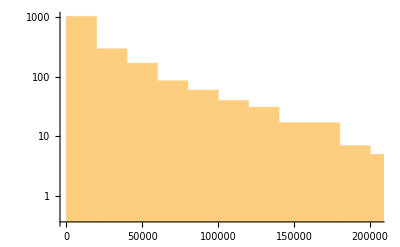

```mathematica
Length[names]
Histogram[FileByteCount/@names,100,ScalingFunctions->"Log"]
```

```mathematica
CodeInspector`Private`$Debug=xTrue;
CodeInspector`Report`Private`$Debug=xTrue;
CodeInspector`Format`Private`$Debug=xTrue;
$DebugLoop=xTrue;
$visuals=xTrue;
CodeInspector`Format`$Interactive=xTrue;
CodeInspector`Format`$NewLintStyle=True;
CodeInspector`Report`$Underlight=xTrue;
```

```mathematica
severityExclusions:={"Formatting","Remark"};
severityExclusions:={"Formatting"};
severityExclusions:={"Formatting","Remark","Warning","Error"};
severityExclusions:={"Formatting","Remark"};
severityExclusions={"Formatting","Remark"};
```

```mathematica
performanceGoal="Speed";
```

```mathematica
tagExclusions:=CodeInspector`Report`$DefaultTagExclusions~Join~{"UnusedVariables","UnusedBlockVariables",
"NotContiguous","StrayLineContinuation","UndocumentedCharacter","ObsoleteSymbol","ExperimentalSymbol"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","DuplicateClauses"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","TopLevel","Blank","ImplicitTimesStrings","DuplicateClauses","PostfixDifferentLine","UnexpectedCharacter","MissingFunction","SystemPatternBlank","DifferentLine"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","TopLevel","Blank","ImplicitTimesStrings","DuplicateClauses","PostfixDifferentLine","UnexpectedCharacter","MissingFunction","SystemPatternBlank","DifferentLine","LogicalConstant","WithArguments","UnexpectedSemicolon","ImplicitTimesBlanks","PrefixPlus","ExpectedSymbol","SuspiciousPrivateContext","SuspiciousRuleFunction","SuspiciousPatternBlankOptional","DotDifferentLine","StrangeCall"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","ModuleArgumentsEmpty","WithArgumentsEmpty","LogicalConstant","CallDifferentLine","DuplicateKeys","DuplicateClauses","InfixBinaryAtQuirk","BlockArgumentsEmpty"};
tagExclusions:={"UnusedVariables","UnusedBlockVariables","ModuleArgumentsEmpty","WithArgumentsEmpty","DuplicateKeys","DuplicateClauses","BlockArgumentsEmpty","MissingFunction"};
tagExclusions={"UnusedVariables"};
```

```mathematica
CodeInspector`Report`Private`$ConfidenceLevel=0.95;
CodeInspector`Report`Private`$MaxConfidenceLevel=1.0;
```

```mathematica
CodeInspector`Private`$fileByteCountMinLimit=0.00*^6;
CodeInspector`Private`$fileByteCountMaxLimit=4.0*^6;
```

```mathematica
CodeInspector`External`$Editor="Sublime Text";
```

```mathematica
$ProcessID
```

27371

```mathematica
start=1;
```

```mathematica
x=start;
file=None;
Print["Linting ", Length[names[[start;;]]]," files"];
Print["Current file: ",Dynamic[Short[file]]];
Print["Current file size: ",Dynamic[FileSize[file]]];
Print["Current index: ",Dynamic[x]];
If[$visuals,
Print[Grid[{
{"concrete parse",Dynamic[CodeParser`Library`$ConcreteParseTime],ProgressIndicator[Dynamic[CodeParser`Library`$ConcreteParseProgress],{0,100}]},
{"aggregate parse",Dynamic[CodeParser`Abstract`$AggregateParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AggregateParseProgress],{0,100}]},
{"abstract parse",Dynamic[CodeParser`Abstract`$AbstractParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AbstractParseProgress],{0,100}]},
{"concrete lint",Dynamic[CodeInspector`$ConcreteLintTime],ProgressIndicator[Dynamic[CodeInspector`$ConcreteLintProgress],{0,100}]},
{"aggregate lint",Dynamic[CodeInspector`$AggregateLintTime],ProgressIndicator[Dynamic[CodeInspector`$AggregateLintProgress],{0,100}]},
{"abstract lint",Dynamic[CodeInspector`$AbstractLintTime],ProgressIndicator[Dynamic[CodeInspector`$AbstractLintProgress],{0,100}]},
{"","",Dynamic[PieChart[{CodeParser`Library`$ConcreteParseTime,CodeParser`Abstract`$AggregateParseTime,CodeParser`Abstract`$AbstractParseTime,CodeInspector`$ConcreteLintTime,CodeInspector`$AggregateLintTime,CodeInspector`$AbstractLintTime},ImageSize->Tiny,ChartLegends->{"concrete parse","aggregate parse","abstract parse","concrete lint","aggregate lint","abstract lint"}]]}
},Alignment->Right]];
];
Print[Row[{"overall",Spacer[10],ProgressIndicator[Dynamic[x],{0,Length[names]}]}]];
Scan[(
file=#;

Which[
TrueQ[$DebugLoop],
Print[x," ",file]
,
Mod[x,100]==0,
Print[x," ",file];
NotebookSave[EvaluationNotebook[]]
];

CodeParser`Library`$ConcreteParseProgress=0;
CodeParser`Abstract`$AggregateParseProgress=0;
CodeParser`Abstract`$AbstractParseProgress=0;
CodeInspector`$ConcreteLintProgress=0;
CodeInspector`$AggregateLintProgress=0;
CodeInspector`$AbstractLintProgress=0;
CodeParser`Library`$ConcreteParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AggregateParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AbstractParseTime=Quantity[0,"Seconds"];
CodeInspector`$ConcreteLintTime=Quantity[0,"Seconds"];
CodeInspector`$AggregateLintTime=Quantity[0,"Seconds"];
CodeInspector`$AbstractLintTime=Quantity[0,"Seconds"];
(*res=lintTest[file,x,"FileNamePrefixPattern"->prefix];*)
(*res=implicitTimesTest[file,x,"FileNamePrefixPattern"->prefix];*)
res=lintTest[file,x,"FileNamePrefixPattern"->prefix];
If[res=!=ok&&$visuals,
Pause[2.0];
];
x++;
)&
,
names[[start;;]]
]//AbsoluteTiming
```

$Aborted

## Symbol Names

```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
(* trigger autoload Failure formatting *)
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

```mathematica
Needs["CodeParser`"]
Needs["CodeParser`CodeAction`"]
```

```mathematica
before=Block[{$ContextPath={"System`"}},Names[]];
```

```mathematica
Needs["CodeInspector`"]
Needs["CodeInspector`ImplicitTimes`"]
Needs["CodeInspector`External`"]
```

```mathematica
after=Block[{$ContextPath={"System`"}},Names[]];
```

```mathematica
Names["CodeInspector`*"]//Column
```

BeginStaticAnalysisIgnore
CodeInspect
CodeInspectBox
CodeInspectBoxSummarize
CodeInspectCST
CodeInspectSummarize
EndStaticAnalysisIgnore
InspectedBoxObject
InspectedBytesObject
InspectedFileObject
InspectedLineObject
InspectedStringObject
InspectionObject
$AbstractLintProgress
$AbstractLintTime
$AggregateLintProgress
$AggregateLintTime
$ConcreteLintProgress
$ConcreteLintTime

```mathematica
uppercaseSymbolQ[name_String]:=UpperCaseQ[StringTake[StringSplit[name,"`"][[-1]],1]]
```

```mathematica
split[name_]:={StringJoin[{#,"`"}&/@Most[#]],Last[#]}&[StringSplit[name,"`"]]
```

```mathematica
Grid[split/@Select[Block[{$ContextPath={"System`"}},Complement[after,before]],uppercaseSymbolQ],Alignment->{Right,Baseline}]
```

CodeInspector` | BeginStaticAnalysisIgnore
CodeInspector` | CodeInspect
CodeInspector` | CodeInspectBox
CodeInspector` | CodeInspectBoxSummarize
CodeInspector` | CodeInspectCST
CodeInspector` | CodeInspectSummarize
CodeInspector` | EndStaticAnalysisIgnore
CodeInspector`External` | OpenInEditor
CodeInspector`Format` | DisableNewLintStyle
CodeInspector`Format` | EnableNewLintStyle
CodeInspector`Format` | LintBold
CodeInspector`Format` | LintContinuation
CodeInspector`Format` | LintEOF
CodeInspector`Format` | LintErrorContinuationIndicator
CodeInspector`Format` | LintErrorIndicator
CodeInspector`Format` | LintMarkup
CodeInspector`Format` | LintPreserve
CodeInspector`Format` | LintSpaceIndicator
CodeInspector`Format` | LintTimes
CodeInspector`ImplicitTimes` | CodeInspectImplicitTimes
CodeInspector`ImplicitTimes` | CodeInspectImplicitTimesSummarize
CodeInspector`ImplicitTimes`Private` | BestImplicitTimesPlacement
CodeInspector`ImplicitTimes`Private` | CodeImplicitTimes
CodeInspector` | InspectedBoxObject
CodeInspector` | InspectedBytesObject
CodeInspector` | InspectedFileObject
CodeInspector` | InspectedLineObject
CodeInspector` | InspectedStringObject
CodeInspector` | InspectionObject
CodeInspector`Summarize` | ListifyLine
FittedModels`FittedModelsCommonDump` | U
FittedModels`FittedModelsCommonDump` | U$
FittedModels`FittedModelsCommonDump` | V
FittedModels`FittedModelsCommonDump` | V$
FittedModels`FittedModelsCommonDump` | W
FittedModels`FittedModelsCommonDump` | W$
SyntaxError` | ExpectedIntegrand
SyntaxError` | ExpectedOperand
SyntaxError` | ExpectedSet
SyntaxError` | ExpectedTilde
SyntaxError` | UnexpectedCloser
System`Private` | OptionsPatternVariable$3526$
System`Private` | OptionsPatternVariable$3530$
System`Private` | OptionsPatternVariable$3532$
System`Private` | OptionsPatternVariable$3534$
System`Private` | OptionsPatternVariable$3535$
System`Private` | OptionsPatternVariable$3536$
System`Private` | OptionsPatternVariable$3537$
System`Private` | OptionsPatternVariable$3538$
System`Private` | OptionsPatternVariable$3539$
System`Private` | OptionsPatternVariable$3540$
System`Private` | OptionsPatternVariable$3541$
System`Private` | OptionsPatternVariable$3542$
System`Private` | OptionsPatternVariable$3545$
System`Private` | OptionsPatternVariable$3546$
System`Private` | OptionsPatternVariable$3548$
System`Private` | OptionsPatternVariable$3550$
Token`Error` | Aborted
Token`Error` | UnterminatedString